# Capital One Coders: Machine learning with Mathematica

### Agenda: 1)Intro to Mathematica 2)iSpy 3)Intro to Machine Learning 4)The Titanic 5)Predicting handwriting (If need more time)?

## Intro to Mathematica - Run the following examples (Shift + enter)

To use Mathematica do the following to run a ‘code block’
1) Click in between the code blocks
2) Click on the plus button between code blocks
3) Click on Wolfram Language Input
4) Type what you want Mathematica to compute
5) Press shift + enter to run your code block

Run the following examples

```mathematica
1+1
```

2

planes above

WolframAlphaQueryResults

WolframAlphaQueryParseResults

5050

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
Plot3D[Cos[y] Sin[y]==Sin[x] Cos[x],{x,-2 Pi,1.5 Pi},{y,-2 Pi,1.5 Pi}]
```

-Graphics3D-

Links to check out some more cool examples

(https://www.wolfram.com/mathematica/new-in-8/free-form-linguistic-input/basic-examples.html) (https://www.wolfram.com/language/gallery/) (https://www.wolframalpha.com/examples/)  (http://demonstrations.wolfram.com/topic.html?limit=20&topic=For+Kids)

Activity: Do one of the following in new code blocks
1) Add two numbers
2) Print a cool 3D Graph
3) Print the satellites above (Wolfram Alpha Query)
4) Print 2 of the examples

## iSpy

We’re going to use the Raspberry Pi camera to have Mathematica recognize images in the room (https://www.wolfram.com/language/11/neural-networks/out-of-core-image-classification.html?product=language) (https://www.wolfram.com/language/11/neural-networks/object-classification.html?product=language) 

For example:

```mathematica
ImageIdentify[-Graphics-]
```

common raccoon

Getting images from your raspberry pi:
1)Type the following into your terminal (./takePhoto) 
2) Drag and drop the photo from your desktop into the empty brackets
3) Type shift + enter

```mathematica
ImageIdentify[]
```

List of items for you to find in the room and identify using your raspberry pi
1) 
2) 
3)

## Intro to Machine Learning (http://blog.stephenwolfram.com/2017/05/machine-learning-for-middle-schoolers/)

```mathematica
SystemOpen["https://www.youtube.com/watch?v=cKxRvEZd3Mw&list=PLT6elRN3Aer7ncFlaCz8Zz-4B5cnsrOMt"]
```

Dataset: The data to train your model on
Features: What your model uses to make predictions
Target variable: What the model is trying to predict
Algorithm / Classifier: How the model comes to a prediction
Learning curve: How quickly the algorithm learns the dataset

Example

```mathematica
Nearest[{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8]},RGBColor[0.8727094319714808,0.9066617343162084,0.09569669807641734],3]
```

{Hue[0.15000000000000002],Hue[0.2],Hue[0.25]}

```mathematica
Nearest[WordList[],"good",10]
```

{good,food,goad,god,gold,goo,goody,goof,goon,goop}

```mathematica
Blur[Rasterize[Style["hello",30]],3]
```

-Graphics-

```mathematica
Table[Blur[-Graphics-, r], {r, 0, 22, 2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ImageIdentify[Blur[-Graphics-, r]], {r, 0, 22, 2}]
```

{cheetah,cheetah,cheetah,cheetah,wildcat,Canada lynx,feline,nutria,musteline mammal,northern river otter,whortleberry,whortleberry}

## Titanic - Predicting survivors

The sinking of the  Titanic is one of the most infamous shipwrecks in history.  On April 15, 1912, during her maiden voyage, the Titanic sank after colliding with an iceberg, killing 1502 out of 2224 passengers and crew. This sensational tragedy shocked the international community and led to better safety regulations for ships.

One of the reasons that the shipwreck led to such loss of life was that there were not enough lifeboats for the passengers and crew. Although there was some element of luck involved in surviving the sinking, some groups of people were more likely to survive than others, such as women, children, and the upper-class.

Today we’re going to have Mathematica figure out a model to determine who survived the Titanic.

```mathematica
SystemOpen["https://www.youtube.com/watch?v=9xoqXVjBEF8"]
```

Lets first see what’s in our data

```mathematica
RandomSample[ResourceData["Sample Data: Titanic Survival"],10]
```

Dataset[<>]

```mathematica
dataset = ExampleData[{"MachineLearning", "Titanic"}, "Data"];
c = Classify[dataset, Method -> "LogisticRegression"]
```

ClassifierFunction[…]

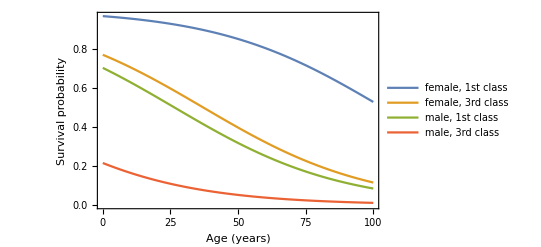

```mathematica
p[class_, age_, sex_] := 
  c[{class, age, sex}, {"Probability", "survived"}];
Plot[{
  p["1st", x, "female"], p["3rd", x, "female"],
  p["1st", x, "male"], p["3rd", x, "male"]}, 
 {x, 0, 100},
 PlotLegends -> {
   "female, 1st class", "female, 3rd class", 
   "male, 1st class", "male, 3rd class"}, 
 Frame -> True,
 FrameLabel -> {"Age (years)", "Survival probability"}]
```

Activity: Create a new classifier that uses the DecisionTree algorithm and see how it performs.

We can also ask Mathematica to determine the best Machine Learning algorithm for us to use, we will do this by not specifying the type of algorithm we want to use, Mathematica will find the best one for us.

```mathematica
dataset = ExampleData[{"MachineLearning", "Titanic"}, "Data"];
c = Classify[dataset]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | {Nominal,Numerical,Nominal}
Classes | ,,diedsurvived
Method | DecisionTree
Accuracy | 78. % ± 2.8 %
Loss | 0.453 ± 0.058
Single evaluation time | 3.1 ms/example
Batch evaluation speed | 69.4 examples/ms
Classifier memory | 308. kB
Training examples used | 1309 examples
Training time | 3.88 s
 |

Now lets use the classifier that we just made to predict our outcome on the titanic

```mathematica
c [{1, 12, male}]
```

survived

```mathematica
datasetMovies = ExampleData[{"MachineLearning", "Satellite"}, "Data"];
```

```mathematica
c = Classify[datasetMovies]
```

ClassifierFunction[…]

```mathematica
dataset
```

dataset